```mathematica
Subscript[Ψ, nlm][r_,θ_,φ_]=ⅇ^(-r/n) √(((2/n)^3 (-l+n-1)!)/(2 n (l+n)!)) ((2 r)/n)^l LaguerreL[-l+n-1,2 l+1,(2 r)/n] SphericalHarmonicY[l,m,θ,φ]
```

2^(1+l) ⅇ^(-r/n) (r/n)^l √(((-1-l+n)!)/(n^4 (l+n)!)) LaguerreL[-1-l+n,1+2 l,(2 r)/n] SphericalHarmonicY[l,m,θ,φ]

```mathematica
K[r_]=Integrate[r^2*(Subscript[Ψ, nlm][r,θ,φ])]
```

```mathematica
Subscript[n, ex(1)][r_]=Integrate[2*Sin[θ]Sum[Abs[Subscript[Ψ, nlm][r,θ,φ]]^2,{n,1,1},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]
```

8 ⅇ^(-2 Re[r])

```mathematica
K[r_]=Subscript[n, ex(1)][r]*r^2
```

8 ⅇ^(-2 Re[r]) r^2

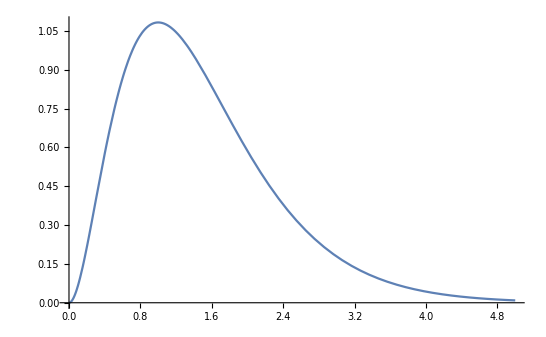

```mathematica
Plot[8 ⅇ^(-2 Re[r]) r^2,{r,0.,5}]
```

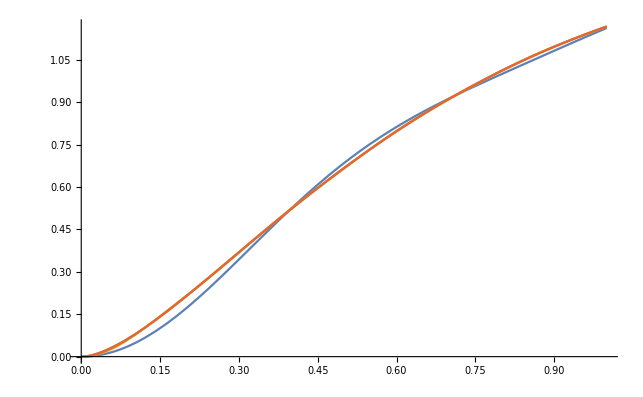

```mathematica
Plot[{(r^2)Sum[1/(2 π r)(x (2/Max[x,0.05]-0.0827625)^2) (Hypergeometric0F1[3,-(2/Max[x,0.05]-0.0827625) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.05]-0.0827625) (x^2+r^2+2 x r)])(0.1),{x,0,2/0.0827625,0.1}],(r^2)Sum[1/(2 π r)(x (2/Max[x,0.005]-0.0827625)^2) (Hypergeometric0F1[3,-(2/Max[x,0.005]-0.0827625) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.005]-0.0827625) (x^2+r^2+2 x r)])(0.01),{x,0,2/0.0827625,0.01}],(r^2)Sum[1/(2 π r)(x (2/Max[x,0.0005]-0.0827625)^2) (Hypergeometric0F1[3,-(2/Max[x,0.0005]-0.0827625) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.0005]-0.0827625) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.0827625,0.001}],(r^2)Sum[1/(2 π r)(x (2/Max[x,0.00005]-0.0827625)^2) (Hypergeometric0F1[3,-(2/Max[x,0.00005]-0.0827625) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.00005]-0.0827625) (x^2+r^2+2 x r)])(0.0001),{x,0,2/0.0827625,0.0001}]},{r,0,1},PlotRange->All]
```